Authors : Souvik Bera and Tanay Pathak
Date : 27th Oct’2022

In this notebook we provide few example of the commands for illustration. This notebook is prepared in Mathematica version 13.1.0

```mathematica
$Version
```

13.1.0 for Microsoft Windows (64-bit) (June 16, 2022)

Setting the directory ::

```mathematica
SetDirectory[NotebookDirectory[]];
```

Calling the package ::

```mathematica
<<HornH1H5`
```

HornH1H5.wl v1.0
Authors : Souvik Bera & Tanay Pathak
There are 22 analytic continuations of Horn H1 and 20 analytic continuations of Horn H5

Examples :: Horn H1

```mathematica
?H1expose
```

```mathematica
H1expose[5]
```

{Abs[x]<x Conjugate[x]&&√Abs[x y]<-Abs[x]+√(1+1/Abs[x]) Abs[x]&&4 Abs[x y]<1&&√Abs[x]<Abs[x]&&√Abs[y/x]<2&&(1+√(1-1/Abs[x])>√Abs[y/x]||(√(-1+Abs[x]))/(√Abs[x])+(√Abs[y])/(√Abs[x])<1||((√(-1+Abs[x]))/(√Abs[x])+(√Abs[y])/(√Abs[x])>1&&√Abs[y/x]≤1)),((-1)^n (-x)^(-a+n) x^-m y^n Gamma[a-b] Gamma[1-a+b] Gamma[1+a-d] Gamma[d] Pochhammer[a,m-n] Pochhammer[c,n] Pochhammer[1+a-d,m-n])/(m! n! Gamma[1+a-b] Gamma[b] Gamma[a-d] Gamma[1-a+d] Pochhammer[1+a-b,m-2 n])+((-1)^(1+n) (-x)^(-b-n) x^-m y^n Gamma[a-b] Gamma[1+b-d] Gamma[d] Pochhammer[b,m+n] Pochhammer[c,n] Pochhammer[1+b-d,m+n])/(m! n! Gamma[a] Gamma[b-d] Gamma[1-b+d] Pochhammer[1-a+b,m+2 n])}

```mathematica
?H1ROC
```

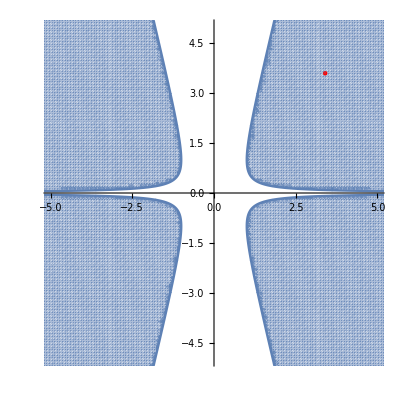

```mathematica
H1ROC[{3.4,3.6},10,{-5,5},resolution-> {150,3}]
```

Examples :: Horn H5

```mathematica
?H5expose
```

```mathematica
H5expose[5]
```

{1/Abs[1-y]<1&&16 Abs[x/(-1+y)^2]<27&&9 Abs[1-y]^2 (2+3 Abs[1-y])+32 Abs[x (-1+y)]<Abs[1-y] (1+√((1+Abs[1-y]) (1+9 Abs[1-y])^3))&&27+√((-9+1/Abs[1-y])^3 (-1+1/Abs[1-y]))>(1+32 Abs[x]+18 Abs[1-y])/Abs[1-y]^2,(4^m x^m (1-y)^(-b-n) (-1+y)^m Gamma[a-b] Gamma[c] Pochhammer[b,-m+n] Pochhammer[1/2 (1+a-c),m] Pochhammer[1/2 (2+a-c),m] Pochhammer[-a+c,-2 m+n])/(m! n! Gamma[a] Gamma[-b+c] Pochhammer[1-a+b,-3 m+n] Pochhammer[-b+c,m])+((-4)^m x^m (1-y)^(-a-n) (-1+y)^(-2 m) Gamma[-a+b] Gamma[c] Pochhammer[a,2 m+n] Pochhammer[1/2 (1+a-c),m] Pochhammer[1/2 (2+a-c),m] Pochhammer[-b+c,m+n])/(m! n! Gamma[b] Gamma[-a+c] Pochhammer[1+a-b,3 m+n] Pochhammer[-b+c,m])}

```mathematica
?H5ROC
```

```mathematica
H5ROC[{3.4,3.6},7,{-5,5},resolution-> {400,5}]
```

-Graphics-